```mathematica
sfile=ReadList["/tmp/snowKoh.dat",String];ndata=(ToExpression/@StringSplit@#&)/@StringReplace[sfile,{"_"->"-"}];
```

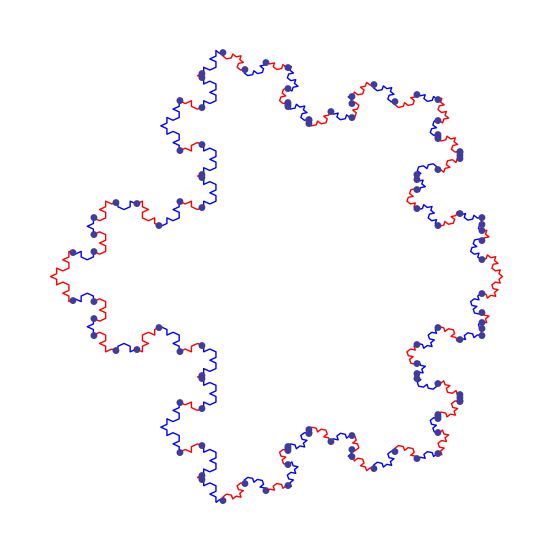

```mathematica
ListLinePlot[ndata, AspectRatio -> 1,PlotMarkers->Automatic,PlotStyle->Thick,Mesh->20,MeshFunctions->{#1&},MeshShading->{Red,Blue},Axes-> False ]
```